1500 x^2-3000 x^3+1500 x^4

1/50

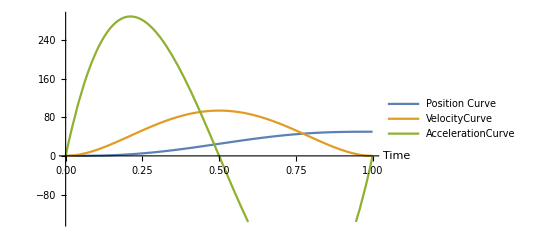

```mathematica
A0=0;
A1=0;
A2=0;
A3=0;
A4=0;
A5=0;
startAngle=0;
finalAngle=50;
startVelocity=0;
finalVelocity=0;
startAcceleration=0;
finalAcceleration=0;
overAllTime =50;
topSpeed =0.1;
A0=startAngle;
A1=startVelocity;
A2=startAcceleration/2;
A3=-1*(20*startAngle-20*finalAngle+12*overAllTime*startVelocity+8*overAllTime*finalVelocity+3*startAcceleration*overAllTime^2-finalAcceleration*overAllTime^2)/(2*overAllTime^3);
A4=(30*startAngle-30*finalAngle+16*overAllTime*startVelocity+14*overAllTime*finalVelocity+3*startAcceleration*overAllTime^2-2*finalAcceleration*overAllTime^2)/(2*overAllTime^4);
A5=-1*(12*startAngle-12*finalAngle+6*overAllTime*startVelocity+6*overAllTime*finalVelocity+startAcceleration*overAllTime^2-finalAcceleration*overAllTime^2)/(2*overAllTime^5);
PositionCurve[t_] :=  A5*t^5+A4*t^4+A3*t^3+A2*t^2+A1*t + A0;
VelocityCurve[t_] :=   PositionCurve'[t];
AccelerationCurve[t_] :=  PositionCurve''[t];
AccelerationCurve[x];
VelocityCurve[x]
eti = overAllTime/finalAngle

MotionGraph = Plot[{PositionCurve[x] ,VelocityCurve[x], AccelerationCurve[x]  }, {x, 0, overAllTime}, PlotLegends->{"Position Curve", "VelocityCurve","AccelerationCurve"}, AxesLabel->{"Time"}]
```

```mathematica
timeDivisionSize =0.2;
timeDivisions = overAllTime / timeDivisionSize;
maxFuncValue = PolyFunction[(timeDivisions/2)*timeDivisionSize]
scalingCoef = topSpeed/maxFuncValue;
transformationFunction [input_] := scalingCoef*input+0;
For[i=0,i≤overAllTime,i+=0.1,
Print[i];
Print[transformationFunction[ PolyFunction[i]]];
]
```

9.375

0

0.

0.1

0.000156816

0.2

0.000614656

0.3

0.0013549

0.4

0.0023593

0.5

0.00361

0.6

0.00508954

0.7

0.00678082

0.8

0.00866714

0.9

0.0107322

1.

0.01296

1.1

0.0153351

1.2

0.0178422

1.3

0.0204666

1.4

0.0231939

1.5

0.02601

1.6

0.0289014

1.7

0.0318547

1.8

0.0348572

1.9

0.0378963

2.

0.04096

2.1

0.0440365

2.2

0.0471145

2.3

0.0501831

2.4

0.0532316

2.5

0.05625

2.6

0.0592284

2.7

0.0621575

2.8

0.0650281

2.9

0.0678317

3.

0.07056

3.1

0.0732051

3.2

0.0757596

3.3

0.0782163

3.4

0.0805686

3.5

0.08281

3.6

0.0849347

3.7

0.086937

3.8

0.0888118

3.9

0.0905543

4.

0.09216

4.1

0.093625

4.2

0.0949455

4.3

0.0961184

4.4

0.0971407

4.5

0.09801

4.6

0.0987241

4.7

0.0992813

4.8

0.0996803

4.9

0.09992

5.

0.1

5.1

0.09992

5.2

0.0996803

5.3

0.0992813

5.4

0.0987241

5.5

0.09801

5.6

0.0971407

5.7

0.0961184

5.8

0.0949455

5.9

0.093625

6.

0.09216

6.1

0.0905543

6.2

0.0888118

6.3

0.086937

6.4

0.0849347

6.5

0.08281

6.6

0.0805686

6.7

0.0782163

6.8

0.0757596

6.9

0.0732051

7.

0.07056

7.1

0.0678317

7.2

0.0650281

7.3

0.0621575

7.4

0.0592284

7.5

0.05625

7.6

0.0532316

7.7

0.0501831

7.8

0.0471145

7.9

0.0440365

8.

0.04096

8.1

0.0378963

8.2

0.0348572

8.3

0.0318547

8.4

0.0289014

8.5

0.02601

8.6

0.0231939

8.7

0.0204666

8.8

0.0178422

8.9

0.0153351

9.

0.01296

9.1

0.0107322

9.2

0.00866714

9.3

0.00678082

9.4

0.00508954

9.5

0.00361

9.6

0.0023593

9.7

0.0013549

9.8

0.000614656

9.9

0.000156816

10.

3.03165×10^-16